```mathematica
hullcurve = 2*Abs[x/2]^3
hull = (x≥-2&&x≤2&&y≥0&&y≤10&&z≥hullcurve&&z≤2)
hullreg = ImplicitRegion[True,{{x,-2,2},{y, 0, 10}, {z, hullcurve, 2}}]
Export["boathull.stl",Region[hullreg]]
hulldensity = 300
waterdensity = 1000
ballastdensity = 5000000/(81*π)
ballast = ImplicitRegion[x^2+(z-0.09)^2≤0.09^2&&y≥0&&y≤10, {x,y,z}]
boatdens = Piecewise[{{ballastdensity+hulldensity, {x,y,z}∈ballast}}, hulldensity]
Show[RegionPlot3D[hullreg,PlotStyle->Directive[Yellow,Opacity[0.5]],Mesh->None], RegionPlot3D[ballast, PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None]]
```

Abs[x]^3/4

x≥-2&&x≤2&&y≥0&&y≤10&&z≥Abs[x]^3/4&&z≤2

ImplicitRegion[-2≤x≤2&&0≤y≤10&&Abs[x]^3/4≤z≤2,{x,y,z}]

boathull.stl

300

1000

5000000/(81 π)

ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]

Piecewise[{{300+5000000/(81 π), {x,y,z}∈ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]}, {300, True}}]

-Graphics3D-

```mathematica
Waterline[θ_]:= ImplicitRegion[z≤Tan[30*π/180]*x+draft,{{x,-2,2}, {y,0,10}, {z,0,2}}]
Mass[boatregion_, boatdensity_]:=Integrate[boatdensity,{x, y, z}∈boatregion]
CenterOfMass[boatregion_, boatdensity_]:= 1/Mass[boatregion, boatdensity]*Integrate[boatdensity * {x,y,z}, {x,y,z}∈boatregion]
CalculateDraft[boatregion_, boatdensity_, θ_]:=NSolve[Integrate[1, {x,y,z}∈RegionIntersection[boatregion, Waterline[θ]]]==Mass[boatregion, boatdensity]/1000, draft][[1]]
DisplacedWater[boatregion_, boatdensity_, θ_]:= RegionIntersection[boatregion, Waterline[θ]]/.CalculateDraft[boatregion, boatdensity, θ]
CenterOfBuoyancy[boatregion_, boatdensity_, θ_]:=1000/Mass[boatregion, boatdensity] * Integrate[{x,y,z}, {x,y,z}∈DisplacedWater[boatregion, boatdensity, θ]]
RightingMoment[boatregion_, boatdensity_, θ_]:=Cross[CenterOfBuoyancy[boatregion, boatdensity, θ]-CenterOfMass[boatregion, boatdensity], Mass[boatregion, boatdensity]*9.8*{-Sin[θ*π/180], 0, Cos[θ*π/180]}]
```

RightingMoment successfully calculates the vector torque exerted by the water on a boat with a hull shape defined by a given region, density as a given function of {x,y,z}, and a given heel angle. Units are in kg and m, to convert to cm and g replace any instance of the number 1000 with the number 1.

Plot of righting moment versus angle for boat from 0 to 180 degrees. The function returns a table of x y and z values for torque every 5 degrees and then fits a 5th degree polynomial (adding more degrees did not change result) and then finds this polynomial’s root to find when torque is zero. It returns the max torque and the angle it occurs as well as the avs.

```mathematica
f[angle_]:=Norm[RightingMoment[hullreg, boatdens,angle]]
angleTable=Parallelize[Table[f[angle],{angle,0,180,5}]]
```

Power::infy: Infinite expression 1/0. encountered.

BooleanRegion::reg: System`TSolveDump`P$8771[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$8771[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$8771[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

BooleanRegion::reg: System`TSolveDump`P$9929[1] is not a correctly specified region.

BooleanRegion::reg: System`TSolveDump`P$8771[1] is not a correctly specified region.

BooleanRegion::reg: System`TSolveDump`P$8769[1] is not a correctly specified region.

BooleanRegion::reg: System`TSolveDump`P$8771[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9929[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9929[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$8771[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$8771[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$8769[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$8769[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$8769[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$8769[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$8771[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$8771[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in ….

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$9312[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9312[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9312[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$10470[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10470[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10470[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$9312[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9312[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9312[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$9310[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9310[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9310[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$9312[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9312[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9312[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$9310[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$9310[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$9310[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$9829[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$10987[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$9829[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$9829[1] is not a correctly specified region.

BooleanRegion::reg: System`TSolveDump`P$9827[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$9827[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

BooleanRegion::reg: System`TSolveDump`P$10346[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10346[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10346[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in ….

BooleanRegion::reg: System`TSolveDump`P$10346[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10346[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10346[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in ….

BooleanRegion::reg: System`TSolveDump`P$10346[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10346[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10346[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

BooleanRegion::reg: System`TSolveDump`P$10344[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10344[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10344[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$10344[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10344[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10344[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in ….

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$10864[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10864[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10864[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$12020[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$12020[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$12020[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in ….

BooleanRegion::reg: System`TSolveDump`P$10864[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10864[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10864[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$10864[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10864[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10864[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$10853[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10853[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10853[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$10853[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$10853[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$10853[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$11381[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$12538[1] is not a correctly specified region.

Integrate::ilim: Invalid integration variable or limit(s) in {x,y,z}∈BooleanRegion[#1&&#2&,{System`TSolveDump`P$12538[1],ImplicitRegion[z≤Times[«2»]+System`TSolveDump`X$12538[«1»]&&-2≤x≤2&&0≤y≤10&&0≤z≤2,{x,y,z}]}].

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

BooleanRegion::reg: System`TSolveDump`P$11381[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$11381[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$11370[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$11370[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

BooleanRegion::reg: System`TSolveDump`P$13055[1] is not a correctly specified region.

General::stop: Further output of BooleanRegion::reg will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

{√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}

```mathematica
bestFit=Fit[angleTable,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Plot[bestFit,{x,0,180}];
ListPlot[angleTable];
Show[%,%%]
root=FindRoot[bestFit,{x,30}];
maxTorque=FindMinimum[bestFit,{x,0}]
avs=root[[1,2]]*5
```

-Graphics-

FindRoot::nlnum: The function value {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {30.}.

FindMinimum::nrnum: The function value 0.+1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] is not a real number at {x} = {0.}.

FindMinimum[bestFit,{x,0}]

FindRoot::nlnum: The function value {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {30.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

5 FindRoot[bestFit,{x,30}]⟦1,2⟧

Below I did it for all 3 axes but the equation returns some wonky results for those values so we should look into that later. Mostly ignore that stuff for now.

3D righting curves we can use later with two angles:

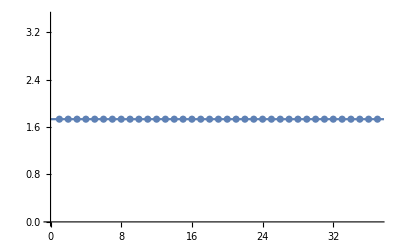

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.73205,{x→0.}}

1.11022×10^-14

-Graphics-

FindRoot::nlnum: The function value {0.+1. Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {0.}.

FindMinimum::nrnum: The function value 0.+1. Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] is not a real number at {x} = {0.}.

FindMinimum[bestFity,{x,0}]

FindRoot::nlnum: The function value {0.+1. Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {0.}.

Part::partd: Part specification FindRoot[bestFity,{x,0}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {0.+1. Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {0.}.

Part::partd: Part specification FindRoot[bestFity,{x,0}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {0.+1. Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]} is not a list of numbers with dimensions {1} at {x} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partd: Part specification FindRoot[bestFity,{x,0}]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

5 FindRoot[bestFity,{x,0}]⟦1,2⟧

Part::partw: Part 3 of √3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::ivar: 0.00367714 is not a valid variable.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::ivar: 0.00367714 is not a valid variable.

General::ivar: 3.67715 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of √3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

Part::partw: Part 3 of 1.732050807568877 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«32»,1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[{√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧],-Graphics-]

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::ivar: 30. is not a valid variable.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::ivar: 30. is not a valid variable.

FindRoot::nlnum: The function value {Fit[{1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],«26»,1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]]}⟦All,3⟧,{1.,«5»},30.]} is not a list of numbers with dimensions {1} at {x} = {30.}.

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::ivar: 30. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

FindRoot::nlnum: The function value {Fit[{1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],«26»,1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]]}⟦All,3⟧,{1.,«5»},30.]} is not a list of numbers with dimensions {1} at {x} = {30.}.

FindRoot[bestFitz,{x,30}]

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

Part::partw: Part 3 of √3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

Fit::fitd: First argument {1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«32»,1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

Part::partw: Part 3 of √3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

General::ivar: 0. is not a valid variable.

FindMinimum::nrnum: The function value … is not a real number at {x} = {0.}.

General::ivar: 0. is not a valid variable.

FindMinimum::nrnum: The function value … is not a real number at {x} = {0.}.

FindMinimum[bestFitz,{x,0}]

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::ivar: 30. is not a valid variable.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::ivar: 30. is not a valid variable.

FindRoot::nlnum: The function value {Fit[{1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],«26»,1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]]}⟦All,3⟧,{1.,«5»},30.]} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFitz,{x,30}]⟦1,2⟧ is longer than depth of object.

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::ivar: 30. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

FindRoot::nlnum: The function value {Fit[{1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],«26»,1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]]}⟦All,3⟧,{1.,«5»},30.]} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFitz,{x,30}]⟦1,2⟧ is longer than depth of object.

Fit::fitd: First argument {√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],«30»,√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]],√3 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]]}⟦All,3⟧ in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

Part::partw: Part 3 of 1.73205 Abs[Det[{{Indeterminate,0.},{Indeterminate,0.}}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {Fit[{1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],«26»,1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]],1.73205 Abs[Det[{«2»}]]}⟦All,3⟧,{1.,«5»},30.]} is not a list of numbers with dimensions {1} at {x} = {30.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partd: Part specification FindRoot[bestFitz,{x,30}]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

5 FindRoot[bestFitz,{x,30}]⟦1,2⟧

```mathematica
bestFitx=Fit[angleTable[[All,1]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFitx,{x,0,180}];
ListPlot[angleTable[[All,1]]];
Show[%,%%]
rootx=FindRoot[bestFitx,{x,0}];
maxTorquex=FindMinimum[bestFitx,{x,0}]
avsx=rootx[[1,2]]*5
bestFity=Fit[angleTable[[All,2]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFity,{x,0,180}];
ListPlot[angleTable[[All,2]]];
Show[%,%%]
rooty=FindRoot[bestFity,{x,0}];
maxTorquey=FindMinimum[bestFity,{x,0}]
avsy=rooty[[1,2]]*5
bestFitz=Fit[angleTable[[All,3]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFitz,{x,0,180}];
ListPlot[angleTable[[All,3]]];
Show[%,%%]
rootz=FindRoot[bestFitz,{x,30}]
maxTorquez=FindMinimum[bestFitz,{x,0}]
avsz=rootz[[1,2]]*5
```

```mathematica
boat2=Import["C:\\Users\\csnow\\Documents\\QEA-Boat\\Boat3.stl","VertexData"];
reg=ConvexHullMesh@boat2
```

-Graphics3D-

```mathematica
centroid=RegionCentroid[reg]
ListPointPlot3D[{centroid}]
Volume[Region[reg]]
```

{206.703,31.2754,82.2862}

-Graphics3D-

2.32208×10^6